```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
Import["Pairs.m"]
```

This is an example for testing GLD and GDX pair cointegration from Jan. 1, 2010 to Dec. 31, 2010.

```mathematica
gld = FinancialData["GLD", {{2010, 1, 1}, {2010, 12, 31}}];
gdx=FinancialData["GDX", {{2010, 1, 1}, {2010, 12, 31}}];
```

Let' s plot the time - series on a chart.  Just because it' s so easy to do so in Mathematica!

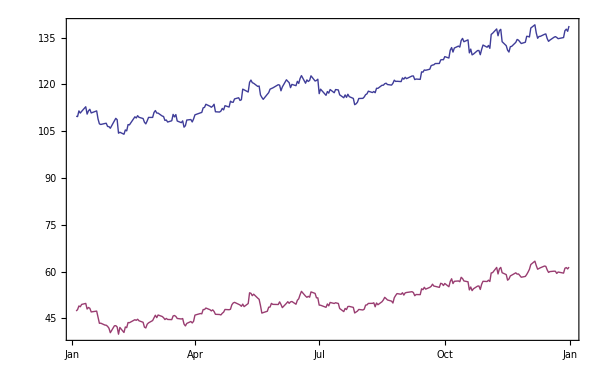

```mathematica
DateListPlot[{gld, gdx}, Joined->True]
```

Next let' s calculate correlations.

```mathematica
Pearson[gld[[All, 2]], gdx[[All, 2]]]
```

0.980367

So GLD/GDX pair is highly correlated.  Let' s see if they are cointegrated.

```mathematica
Cointegrate[gld[[All, 2]], gdx[[All, 2]]]
```

InterpolatingFunction::dmval: Input value TraditionalForm`{-4.33857} lies outside the range of data in the interpolating function. Extrapolation will be used.

ADF::toosmall: p-value smaller than printed value

0.01

This show that GLD/GDX pair has 99 % probability for cointegration